```mathematica
ClearAll["Global`*"];
```

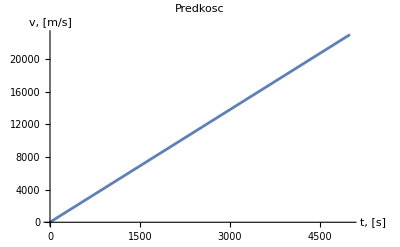

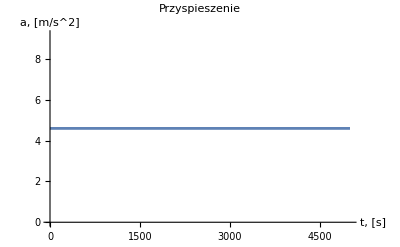

0.+41400. t+9522. t^2

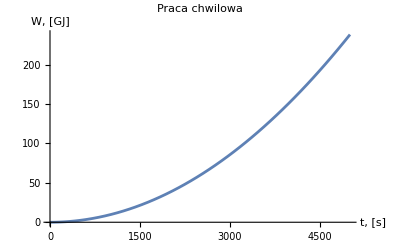

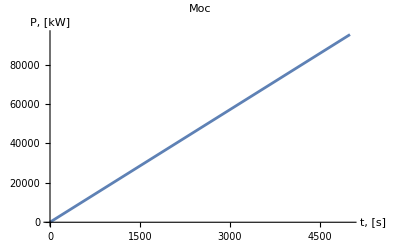

```mathematica
a1 := 2.3
a2 := 10
s = a1*t^2 + a2*t;
velocity = D[s,t];
tmax = 5000;
Plot[velocity, {t, 0 ,tmax},AxesLabel->{"t, [s]","v, [m/s]"},PlotLabel->"Predkosc"]
accel =  D[velocity,t];
Plot[accel, {t, 0 ,tmax},AxesLabel->{"t, [s]","a, [m/s^2]"},PlotLabel->"Przyspieszenie"]
m = 900;
work = ∫_0^t accel*m*vⅆt;
Plot[work*10^(-9), {t, 0 ,tmax},AxesLabel->{"t, [s]","W, [GJ]"},PlotLabel->"Praca chwilowa"]
power = D[work,t];
Plot[power*10^-3, {t, 0 ,tmax},AxesLabel->{"t, [s]","P, [kW]"},PlotLabel->"Moc"]
```